# Analysis of Epidemic output

## Basic parameters

```mathematica
demeCount=1;
```

```mathematica
demes={"world"};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Dropbox/current-projects/phylodynamics-presentation/epidemic

```mathematica
spatialColors={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

```mathematica
spatialColors=Map[Lighter[#,0.1]&,spatialColors]
```

{RGBColor[0.7885,0.7552,0.3466],RGBColor[0.3916,0.6481,0.7372],RGBColor[0.8713,0.2179,0.2188]}

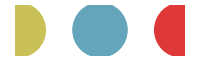

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,spatialColors]},PlotRange->All,AspectRatio->0.3,ImageSize->200]
```

```mathematica
spatialColorRules=MapIndexed[#2[[1]]-1->#1&,spatialColors];
```

```mathematica
sirColors={RGBColor[0.765,0.728,0.274],RGBColor[0.857,0.131,0.132],RGBColor[0.324,0.609,0.708],RGBColor[0.471,0.109,0.527]};
```

```mathematica
sirColors=Map[Lighter[#,0.1]&,sirColors];
```

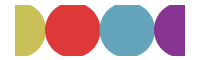

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,sirColors]},PlotRange->All,AspectRatio->0.3,ImageSize->200]
```

```mathematica
sirColorRules=MapThread[#1->#2&,{{"S","I","R","Cases"},sirColors}];
```

## Options

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize];
```

```mathematica
SetOptions[ContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize];
```

```mathematica
SetOptions[DiscretePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->imageSize,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->imageSize,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

## Timeseries

```mathematica
timeseriesPlot[list_,col_,ylabel_,range_,ticks_]:=ListLinePlot[list,AspectRatio->0.3,ImageSize->300,Filling->Axis,PlotStyle->Darker[col,0.3],FillingStyle->Lighter[col,0.6],FrameLabel->{"Year",ylabel},ImagePadding->{{55,5},{30,5}},FrameTicks->ticks,PlotRange->range]
```

```mathematica
timeseriesPlot[list_,exp_,colList_,colExp_,ylabel_,range_,ticks_]:=ListLinePlot[{list,exp},AspectRatio->0.3,ImageSize->300,Filling->1->Axis,PlotStyle->{Darker[colList,0.3],Directive[Dashed,Thick,colExp]},FillingStyle->Lighter[colList,0.6],FrameLabel->{"Year",ylabel},ImagePadding->{{55,5},{30,5}},FrameTicks->ticks,PlotRange->range]
```

```mathematica
frameTicks[xMin_,xMax_,yMin_,yMax_,xTicksStep_,yTicksStep_]:={{Table[{i, NumberForm[N[i],ExponentFunction->(If[-5<#<5,Null,#]&)], {0, 0.01}}, {i, Floor[yMin,yTicksStep], Ceiling[yMax,yTicksStep], yTicksStep}], None}, {Table[{i, i, {0, 0.01}}, {i,Floor[xMin,xTicksStep], Ceiling[xMax,xTicksStep], xTicksStep}], None}}
```

### Data import

Assuming weekly output

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,data[[1]]]
```

{date→1,div→2,tmrca→3,netau→4,serialInterval→5,totalN→6,totalS→7,totalI→8,totalR→9,totalCases→10,worldDiv→11,worldTmrca→12,worldNetau→13,worldN→14,worldS→15,worldI→16,worldR→17,worldCases→18}

```mathematica
data=Drop[data,1];
```

```mathematica
date="date"/.headerRules;
```

```mathematica
popSize=1000000;
```

```mathematica
beta=0.3;
```

### Susceptibles

```mathematica
index="totalS"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

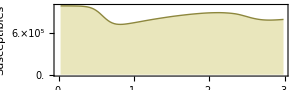

```mathematica
fig=timeseriesPlot[list,sirColors[[1]],"Susceptibles",{0,All},frameTicks[0,3,0,1000000,0.5,200000]]
```

```mathematica
Export["susceptibles.pdf",fig,"PDF"]
```

susceptibles.pdf

### Infecteds

```mathematica
index="totalI"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

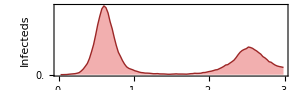

```mathematica
fig=timeseriesPlot[list,sirColors[[2]],"Infecteds",{0,All},frameTicks[0,3,0,1000000,0.5,3000]]
```

```mathematica
Export["infecteds.pdf",fig,"PDF"]
```

infecteds.pdf

### Recovereds

```mathematica
index="totalR"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

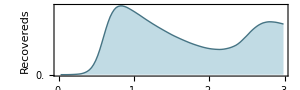

```mathematica
fig=timeseriesPlot[list,sirColors[[3]],"Recovereds",{0,All},frameTicks[0,3,0,1000000,0.5,100000]]
```

```mathematica
Export["recovereds.pdf",fig,"PDF"]
```

recovereds.pdf

### Cases

```mathematica
index="totalCases"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

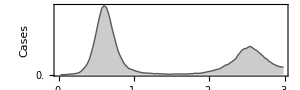

```mathematica
fig=timeseriesPlot[list,Gray,"Cases",{0,All},frameTicks[0,3,0,1000000,0.5,5000]]
```

```mathematica
Export["cases.pdf",fig,"PDF"]
```

cases.pdf

### Diversity

```mathematica
index="div"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

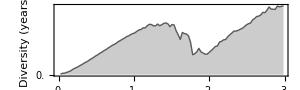

```mathematica
fig=timeseriesPlot[list,Gray,"Diversity (years)",{0,All},frameTicks[0,3,0,10,0.5,1]]
```

```mathematica
Export["diversity.pdf",fig,"PDF"]
```

diversity.pdf

### TMRCA

```mathematica
index="tmrca"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

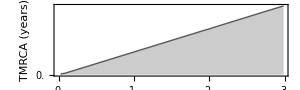

```mathematica
fig=timeseriesPlot[list,Gray,"TMRCA (years)",{0,All},frameTicks[0,3,0,10,0.5,1]]
```

```mathematica
Export["tmrca.pdf",fig,"PDF"]
```

tmrca.pdf

### Serial interval

Expect 1/(β S/N)=N/(β S)

```mathematica
index="serialInterval"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],365*data[[All,index]]-0.5}];
```

```mathematica
exp=Transpose[{data[[All,date]],popSize/(beta*data[[All,"totalS"/.headerRules]])}];
```

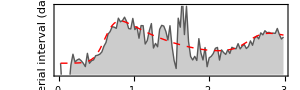

```mathematica
fig=timeseriesPlot[list,exp,Gray,Red,"Serial interval (days)",{3,5},frameTicks[0,3,0,10,0.5,1]]
```

```mathematica
Export["serial_interval.pdf",fig,"PDF"]
```

serial_interval.pdf

### N_e τ (serial interval)

Expect I/(β S/N)=(I N)/(2β S)

```mathematica
index="netau"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

```mathematica
exp=Transpose[{data[[All,date]],(data[[All,"totalI"/.headerRules]]*popSize)/(1.2*2*365*beta*data[[All,"totalS"/.headerRules]])}];
```

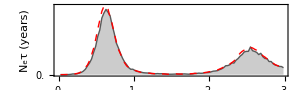

```mathematica
fig=timeseriesPlot[list,exp,Gray,Red,"N_eτ (years)",{0,All},frameTicks[0,3,0,1000,0.5,10]]
```

```mathematica
Export["netau.pdf",fig,"PDF"]
```

netau.pdf

### N_e τ (incidence)

Expect I^2/(2 f)

```mathematica
index="netau"/.headerRules;
```

```mathematica
list=Transpose[{data[[All,date]],data[[All,index]]}];
```

```mathematica
exp=Transpose[{data[[All,date]],(10*data[[All,"totalI"/.headerRules]]^2)/(2*365*data[[All,"totalCases"/.headerRules]])}];
```

```mathematica
exp=Transpose[{data[[All,date]],(10*data[[All,"totalI"/.headerRules]]^2)/(1.2*2*365*Append[data[[2;;-1,"totalCases"/.headerRules]],data[[-1,"totalCases"/.headerRules]]])}];
```

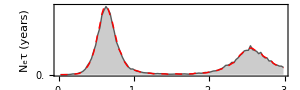

```mathematica
fig=timeseriesPlot[list,exp,Gray,Red,"N_eτ (years)",{0,All},frameTicks[0,3,0,1000,0.5,10]]
```

```mathematica
Export["netau.pdf",fig,"PDF"]
```

netau.pdf

## Tree

### Data import

First node is child, second is parent

```mathematica
branchScale=0.001;tipScale=0.0015;clip=0.005;
```

```mathematica
getThickness[count_]:=Thickness[Clip[branchScale*N[Sqrt[count]],{0,clip}]]
```

```mathematica
getPointSize[count_]:=PointSize[N[tipScale*Sqrt[count]]];
```

```mathematica
name=1;year=2;trunk=3;tip=4;mark=5;loc=6;layout=7;
```

```mathematica
branchData=ToExpression[Import["out.branches","Table"]];
```

```mathematica
branchData[[1]]
```

{{40dea6bc,0.,1,0,1,0,46.236},{2d04cf67,0.,1,0,1,0,46.236},1083}

```mathematica
Length[branchData]
```

6633

### Distribution of tips

```mathematica
tips=Cases[branchData[[All,1]],x_/;x[[tip]]==1];
```

```mathematica
Length[tips]
```

908

```mathematica
tips[[All,{year,layout}]];
```

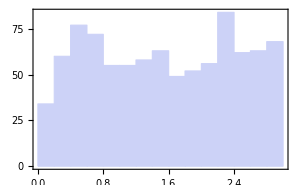

```mathematica
Histogram[tips[[All,year]]]
```

### Time vs Layout

```mathematica
branchLines=Map[{Thickness[0.0025],Gray,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipPoints={Black,Map[Point,tips[[All,{year,layout}]]]};
```

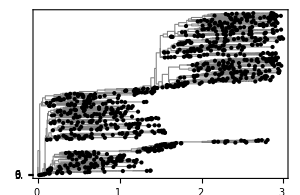

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->0.65,PlotRange->All,FrameLabel->{"Year"},Frame->{True,False,False,False},FrameTicks->frameTicks[0,3,0,10,0.5,1]]
```

```mathematica
Export["tree.pdf",fig,"PDF"]
```

tree.pdf